# Lab 4: Resonant Harmonic Motion Christopher Greene, Michael Imbimbo, Henry Davis

## Simulation 1

0.429

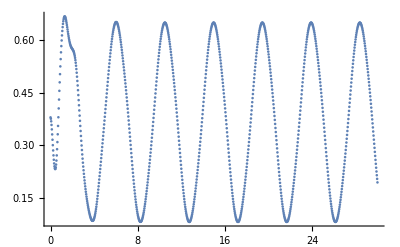

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω0 = 1.405;
ϕ=3.733;
b=0.2596;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq-b*Sin[ω0*t-ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim1.csv",modeldata]
```

Sim1.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim1.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar1 = 0.2790;
ϕr1 = 0.9281;
ωr1 = 1.405;
```

## Simulation II

0.429

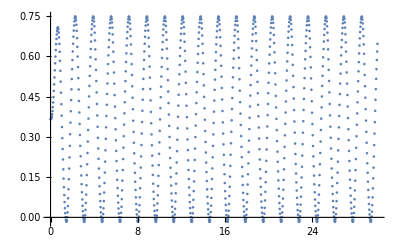

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
xeq=0.366;
x=xeq;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω0 = 3.824;
ϕ=3.082;
b=0.2582;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq-b*Sin[ω0*t-ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim2.csv",modeldata]
```

Sim2.csv

```mathematica
Ar2 = 0.3793;
ϕr2 = 5.527;
ωr2 = 3.824;
```

## Simulation III

0.429

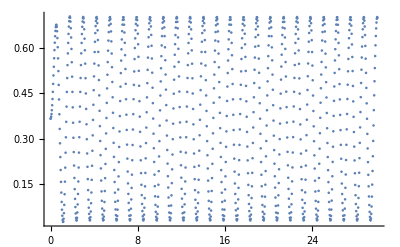

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
xeq=0.366;
x=xeq;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω0 = 5.124;
ϕ=2.813;
b=0.2641;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq-b*Sin[ω0*t-ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim3.csv",modeldata]
```

Sim3.csv

```mathematica
Ar3 = 0.3347;
ϕr3 = 5.119;
ωr3 = 5.124;
```

Follow the same pattern for the rest of the trials.  Make sure that you do the sine fit for late time data (so that the weirdness of the beginning doesn’t make the fit worse.)  After all 10 trials are done, we need to plot ω0 vs ωr, Ar vs ω0, and ϕr vs ω0.  To get the value for b, you do a Sine fit of the angle plot (blue) in the trial data files.  Section 3.6 in the book is what we are doing, so the plots hopefully will look similar to those.